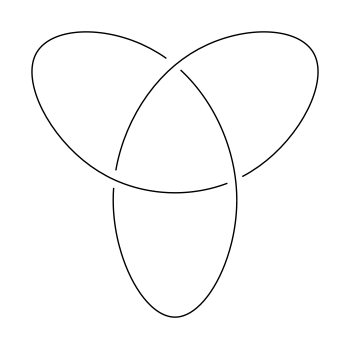
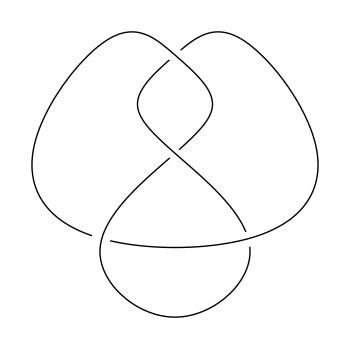
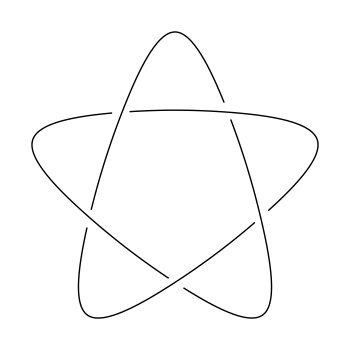
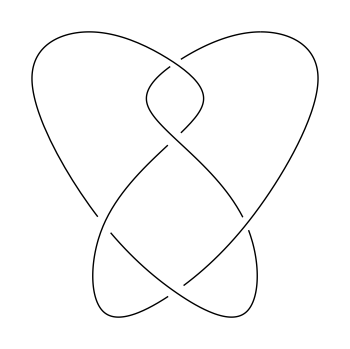
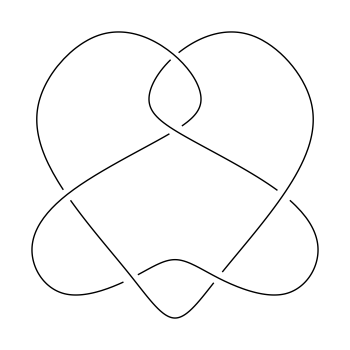
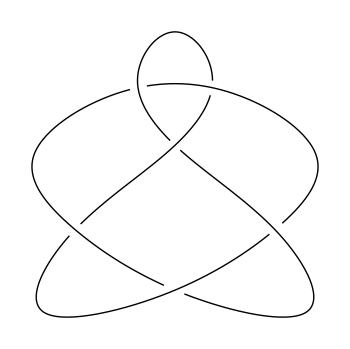
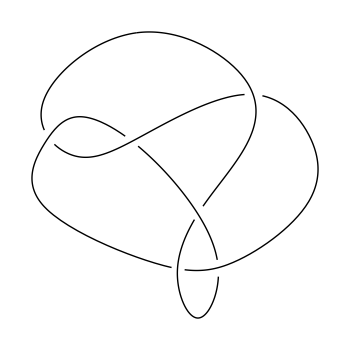
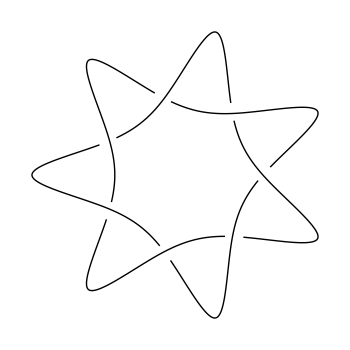

```mathematica
Column[Table[ Show[Graphics[KnotData[x,"KnotDiagram"]], ImageSize->350],{x,Take[KnotData[All],{2,25}]}],Spacings->5]
```

```mathematica
<<ComputationalGeometry`
```

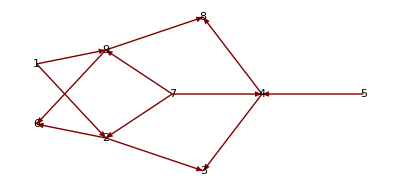

```mathematica
GraphPlot[{1->2,2->3,4->3,5->4,2->6,7->2,7->4,4->8,1->9,9->6,7->9,9->8},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
Wikipedia challenge for unknot :
```

```mathematica
GraphPlot[{1->15,2->1,4->1,2->3,7->2,5->2,3->15,8->3,5->4,4->10,5->11,6->5,6->12,6->7,6->12,7->8,7->11,8->9,8->13,9,15,11->10,10->15,12->11,11->15,11->14,13->15,14->15},DirectedEdges->True,VertexLabeling->True]
```

GraphPlot::grph: {1 → 15, 2 → 1, 4 → 1, 2 → 3, 7 → 2, 5 → 2, 3 → 15, 8 → 3, 5 → 4, 4 → 10, 5 → 11, 6 → 5, 6 → 12, 6 → 7, 6 → 12, 7 → 8, 7 → 11, 8 → 9, 8 → 13, 9, 15, 11 → 10, 10 → 15, 12 → 11, 11 → 15, 11 → 14, 13 → 15, 14 → 15} is not a valid graph.

```mathematica
GraphPlot[{1->15,2->1,4->1,2->3,7->2,5->2,3->15,8->3,5->4,4->10,5->11,6->5,6->7,6->12,7->8,7->11,8->9,8->13,9->15,11->10,10->15,12->11,11->15,11->14,13->15,14->15},DirectedEdges->True,VertexLabeling->True, Method->"RadialDrawing"]
```

GraphPlot::mthd: The value of option Method -> "ElectricalEmbedding" should be Automatic, "SpringElectricalEmbedding", "SpringEmbedding", "LayeredDrawing", "LayeredDigraphDrawing", "RadialDrawing", "HighDimensionalEmbedding", "CircularEmbedding", "SpiralEmbedding", "LinearEmbedding", or "RandomEmbedding".

GraphPlot::grph: {1 → 15, 2 → 1, 4 → 1, 2 → 3, 7 → 2, 5 → 2, 3 → 15, 8 → 3, 5 → 4, 4 → 10, 5 → 11, 6 → 5, 6 → 7, 6 → 12, 7 → 8, 7 → 11, 8 → 9, 8 → 13, 9 → 15, 11 → 10, 10 → 15, 12 → 11, 11 → 15, 11 → 14, 13 → 15, 14 → 15} is not a valid graph.

```mathematica
Graph[{1->15,2->1,4->1,2->3,7->2,5->2,3->15,8->3,5->4,4->10,5->11,6->5,6->7,6->12,7->8,7->11,8->9,8->13,9->15,11->10,10->15,12->11,11->13,11->15,11->14,13->15,14->15},DirectedEdges->True, GraphLayout->"PlanarEmbedding",VertexLabels->Table[i->i,{i,15}], VertexLabelStyle->Directive[FontFamily->"Consolas",Red,Italic,20], VertexStyle->Red,VertexSize->  Large, EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.03}]]
```

-Graphics-

```mathematica
Graph[{1->15,2->1,4->1,2->3,7->2,5->2,3->15,8->3,5->4,4->10,5->11,6->5,6->7,6->12,7->8,7->11,8->9,8->13,9->15,11->10,10->15,12->11,11->13,11->15,11->14,13->15,14->15},DirectedEdges->True, VertexLabels->Table[i->i,{i,15}], VertexLabelStyle->Directive[FontFamily->"Consolas",Red,Italic,20], VertexStyle->Red,VertexSize->  Normal]
```

-Graphics-